### Osc dependency matrix and frequencies

```mathematica
mat=Boole[Outer[SubsetQ[#2,#1]&,
Values[$LifeParts["Oscillator"]],
Values[$LifeParts["Oscillator"]],
1]];
```

Values::invrl: The argument $LifeParts[Oscillator] is not a valid Association or a list of rules.

Values::invrl: The argument True is not a valid Association or a list of rules.

General::stop: Further output of Values::invrl will be suppressed during this calculation.

```mathematica
diffs = DeleteCases[Position[mat,1],{x_,x_}];
```

Matrix of all oscillator dependencies

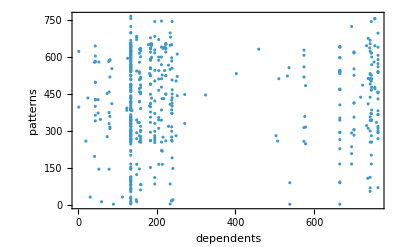

```mathematica
ListPlot[diffs, Frame-> True, FrameLabel->{"dependents", "patterns"}]
```

Winner take-all effects

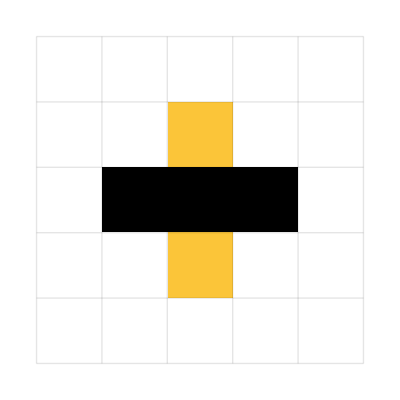
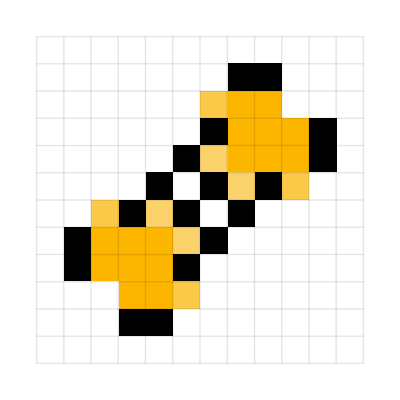
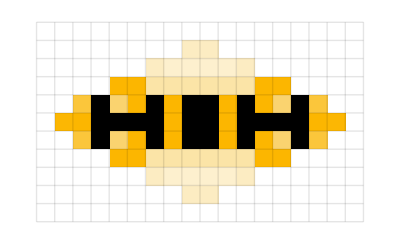
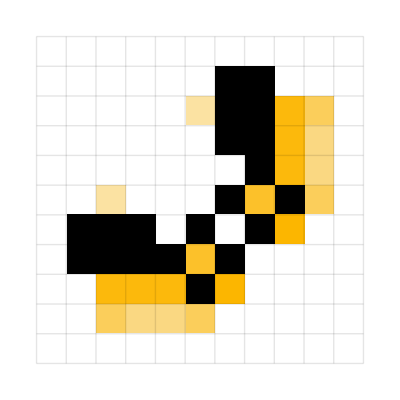
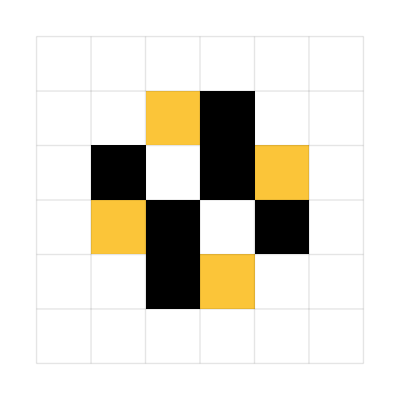
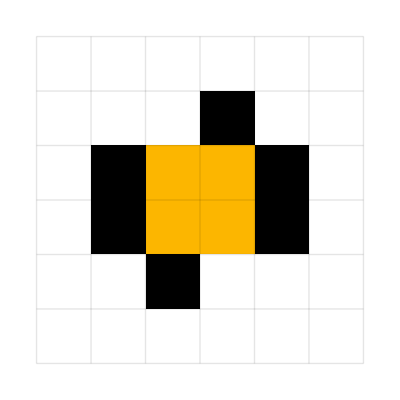
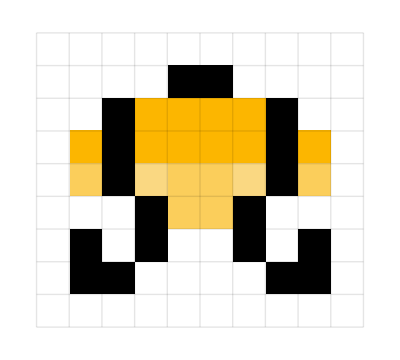
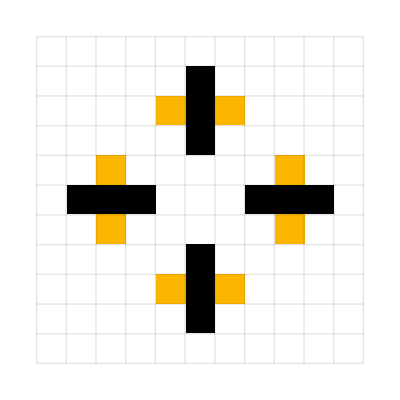
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
t10 = CellularAutomatonHistoryPlot["GameOfLife", {#[[-1]], 0}, 2Length[#]]&/@Values[$LifeParts["Oscillator"]][[TakeLargestBy[Range[Length[mat]], Total[mat[[#]]]&, 20]]]
```

```mathematica
With[{tots = ReverseSort[Total/@ mat]},
ListLogLogPlot[ReplacePart[tots,Table[i-> Callout[tots[[i]], t10[[i]]], {i, 1, 20}]], Frame-> True, FrameLabel->{"oscillator", "frequency (log)"} ]
 ]
```

-Graphics-

#### How are these guys used?

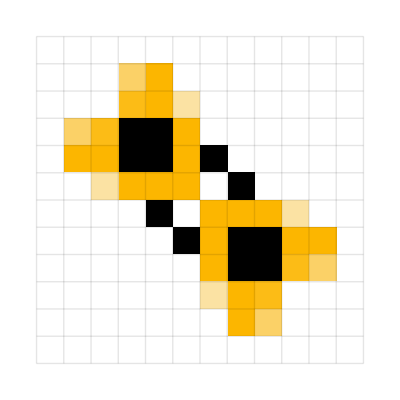

```mathematica
CellularAutomatonHistoryPlot["GameOfLife", {#MatrixData, 0}, #Period]&[$LifeData[Keys[$LifeParts["Oscillator"]][[TakeLargestBy[Range[Length[mat]], Total[mat[[#]]]&, 20][[2]]]]]]
```

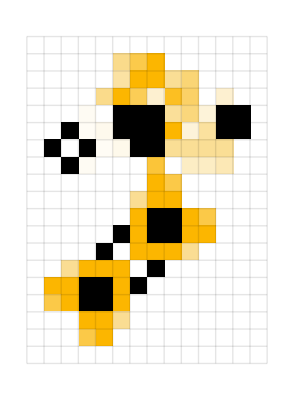
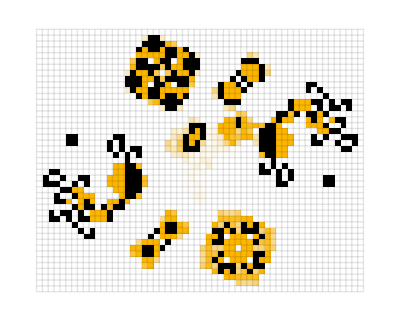
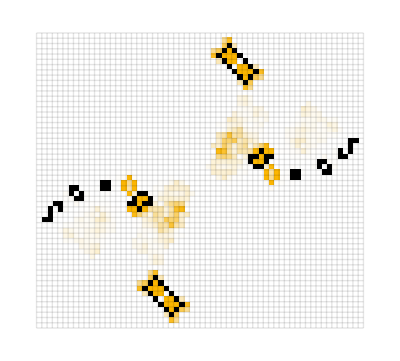
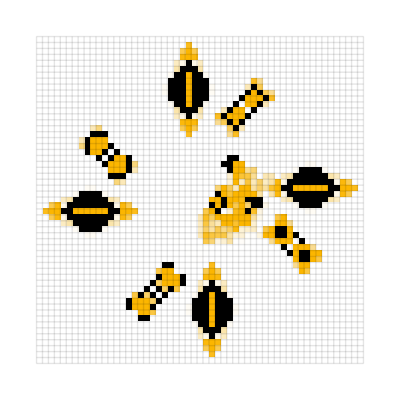
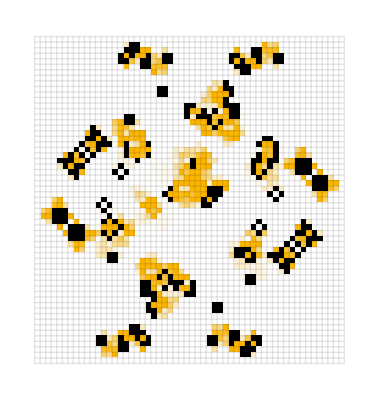
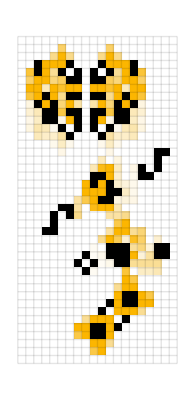
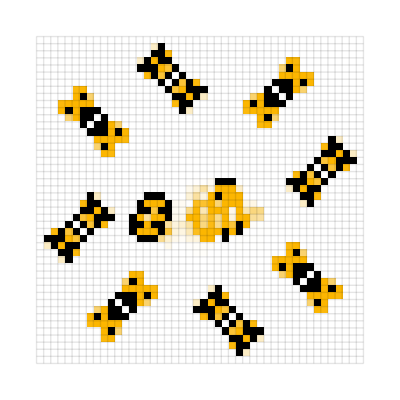
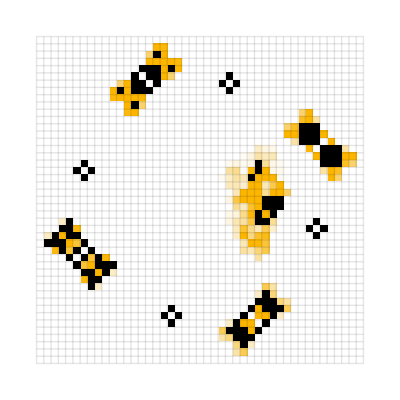
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
CellularAutomatonHistoryPlot["GameOfLife", {#MatrixData, 0}, #Period]&[$LifeData[#]]&/@ Keys[$LifeParts["Oscillator"]][[Catenate[Position[mat[[TakeLargestBy[Range[Length[mat]], Total[mat[[#]]]&, 20][[2]]]], 1]]]]
```

#### highlighted bounding box graph

TODO: Need to deal with rotation, because the current method is not matching on different orientations

```mathematica
names = ;
```

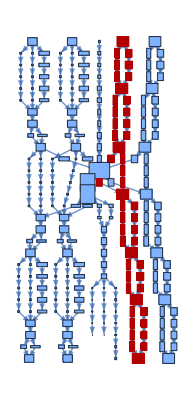

```mathematica
HighlightGraph[#[[2]], 
VertexList[#[[2]]][[
(Function[{left, right},With[{common=Intersection[left,right]},{Flatten[Position[left,#]&/@common],Flatten[Position[right,#]&/@common]}]]@@
(Map[
(SparseArray[
Thread[
(Transpose[{#[[All, 1]] -  Min[#[[All, 1]]]+1, #[[All, 2]] -  Min[#[[All, 2]]]+1}]&[
Ramp[#[[-1]] ]]+ 1)->1]]&), 
VertexList/@ #, {2}]))[[2]]]]]&/@ Map[BoundingBoxLayeredGraph[$LifeData[#]]&, names[[{1}]], {2}]
```

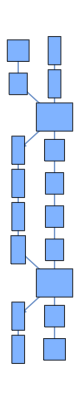
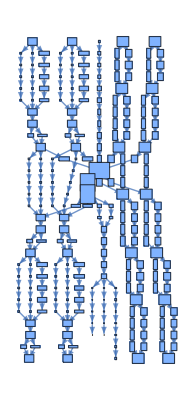

```mathematica
Map[BoundingBoxLayeredGraph[$LifeData[#]]&, names[[{1}]], {2}]
```

```mathematica
HighlightGraph[#[[2]], 
VertexList[#[[2]]][[
(Function[{left, right},With[{common=Intersection[left,right]},{Flatten[Position[left,#]&/@common],Flatten[Position[right,#]&/@common]}]]@@
(Map[
(SparseArray[
Thread[
(Transpose[{#[[All, 1]] -  Min[#[[All, 1]]]+1, #[[All, 2]] -  Min[#[[All, 2]]]+1}]&[
Ramp[#[[-1]] ]]+ 1)->1]]&), 
VertexList/@ #, {2}]))[[2]]]]]&/@ Map[BoundingBoxLayeredGraph[$LifeData[#]]&, {{"Charity's p16"}}, {2}]
```

Part::partw: Part 2 of … does not exist.

VertexList::graph: A graph object is expected at position 1 in ….

Function::fpct: Too many parameters in {left,right} to be filled from ….

$Aborted[]

General::stop: Further output of Part::partw will be suppressed during this calculation.

$Aborted[]

$Aborted

```mathematica
HighlightGraph[#[[2]], 
VertexList[#[[2]]][[
(Function[{left, right},With[{common=Intersection[left,right]},{Flatten[Position[left,#]&/@common],Flatten[Position[right,#]&/@common]}]]@@
(Map[
(SparseArray[
Thread[
(Transpose[{#[[All, 1]] -  Min[#[[All, 1]]]+1, #[[All, 2]] -  Min[#[[All, 2]]]+1}]&[
Ramp[#[[-1]] ]]+ 1)->1]]&), 
VertexList/@ #, {2}]))[[2]]]]]Keys[$LifeParts["Oscillator"]][[Catenate[Position[mat[[TakeLargestBy[Range[Length[mat]], Total[mat[[#]]]&, 20][[2]]]], 1]]]]
```

{Charity's p16,Figure eight,p104lumpsofmuckshuttle,p104rpentominohassler,p120rpentominohassler,p144uturnerhassler,p16centuryhassler,p224 lumps of muck hassler,p280 U-turner hassler,p32 blinker hassler 2,p32 honey farm hassler,p40honeyfarmhassler,p48prepulsarshuttle,p48 toad hassler,p56c2honeyfarmhassler,p56honeyfarmhassler,p64honeyfarmhassler,p64honeyfarmhassler2,p64rpentominohassler2,p64 thunderbird hassler,p72centurylomhassler,p72honeyfarmhassler2,p72lumpsofmuckhassler,p72 quasi-shuttle,p80procrastinatorhassler,p88lumpsofmuckhassler,p88lumpsofmuckhassler2,p88rpentominoshuttle,p96 honey farm hassler,p96honeyfarmhassler2,p96honeyfarmhassler3,prepulsarshuttle40}

```mathematica
BoundingBoxLayeredGraph[$LifeData[#], 10]&/@ Take[Keys[$LifeParts["Oscillator"]][[Catenate[Position[mat[[TakeLargestBy[Range[Length[mat]], Total[mat[[#]]]&, 20][[2]]]], 1]]]], 2]
```

Keys::invrl: The argument If[10==Automatic,Min[<|Name→Charity's p16,Year→2022,Class→Oscillator,Period→16,Wiki→https://conwaylife.com/wiki/Unix_on_Charity%27s_p16,DataFiles→{charitysp16.cells,charitysp16.rle},MatrixData→«1»,InitialWeight→28|>[Period],5000],10] is not a valid Association or a list of rules.

Union::heads: Heads Rule and List at positions 2 and 1 are expected to be the same.

Merge::list1: The argument MultiwayLife[<|1→<|Data→{{7,5},{7,6},{8,5},{8,6},{8,8},{9,9},{10,6},{11,7},{11,9},{11,10},{12,9},{12,10}},InComponents→{}|>,2→<|Data→{{1,6},{1,7},{1,8},{2,6},{2,7},{2,8},{2,11},{3,6},{3,7},{3,10},{3,12},{4,11}},InComponents→{}|>,3→<|Data→{{1,1},{1,2},{2,1},{2,2}},InComponents→{}|>|>,If[10==Automatic,Min[«1»],10]] is not a valid list of Associations or rules or lists of rules.

Keys::invrl: The argument Association[Union@@MapIndexed[Thread[#1→Slot[«1»]⟦1⟧]&,Keys/@MultiwayLife[<|1→<|Data→{{7,5},{7,6},{8,5},{8,6},{8,8},{9,9},{10,6},{11,7},{11,9},{11,10},{12,9},{12,10}},InComponents→{}|>,2→«1»,3→<|Data→{{1,1},{1,2},{2,1},{2,2}},InComponents→{}|>|>,If[10==Automatic,Min[<|«8»|>[«1»],5000],10]]]] is not a valid Association or a list of rules.

Merge::argx: Merge[MultiwayLife[<|1→<|Data→{{7,5},{7,6},{8,5},{8,6},{8,8},{9,9},{10,6},{11,7},{11,9},{11,10},{12,9},{12,10}},InComponents→{}|>,2→<|Data→{{1,6},{1,7},{1,8},{2,6},{2,7},{2,8},{2,11},{3,6},{3,7},{3,10},{3,12},{4,11}},InComponents→{}|>,3→<|Data→{{1,1},{1,2},{2,1},{2,2}},InComponents→{}|>|>,If[10==Automatic,«1»,10]],«5»] called with 2 arguments; 1 argument is expected.

KeyValueMap::invak: The argument If[10==Automatic,Min[<|Name→Charity's p16,Year→2022,Class→Oscillator,Period→16,Wiki→https://conwaylife.com/wiki/Unix_on_Charity%27s_p16,DataFiles→{charitysp16.cells,charitysp16.rle},MatrixData→«1»,InitialWeight→28|>[Period],5000],10] is not a valid Association.

Values::invrl: The argument Association[(#1→{strat$2442476[#1],#1,merge$2442476[#1,Data]}&)/@vertices$2442476] is not a valid Association or a list of rules.

LayeredGraph::graph: A graph object is expected at position 1 in LayeredGraph[Graph[Values[Association[(Slot[«1»]→{«3»}&)/@vertices$2442476]],Catenate[MultiwayLife[{},Catenate[KeyValueMap[Function[{«2»},Map[«2»]],If[Equal[«2»],Min[«2»],10]]]]]],VertexShapeFunction→Function[{pos,val,blah},(Rectangle[pos-Times[«2»],pos+Slot[«1»] Power[«2»]]&)[(Subtract@@Reverse[«1»]&)/@(«1»)^T]]].

Keys::invrl: The argument If[10==Automatic,Min[<|Name→Figure eight,Year→1970,Class→Oscillator,Period→8,«1»,DataFiles→{figureeight.cells,figureeight.rle},MatrixData→SparseArray[Automatic,{6,6},0,{1,{{0,2,5,6,7,10,12},{{1},{2},{1},{2},{4},{5},{2},{3},{5},{6},{5},{6}}},{1,1,1,1,1,1,1,1,1,1,1,1}}],InitialWeight→12|>[Period],«4»],10] is not a valid Association or a list of rules.

General::stop: Further output of Keys::invrl will be suppressed during this calculation.

Union::heads: Heads Rule and List at positions 2 and 1 are expected to be the same.

Merge::list1: The argument MultiwayLife[<|1→<|Data→{{1,5},{1,6},{2,3},{2,5},{2,6},{3,2},{4,5},{5,1},{5,2},{5,4},{6,1},{6,2}},InComponents→{}|>|>,If[10==Automatic,Min[<|Name→Figure eight,Year→1970,Class→Oscillator,Period→8,Wiki→h…t,DataFiles→{figureeight.cells,figureeight.rle},MatrixData→«1»,InitialWeight→12|>[Period],«4»],10]] is not a valid list of Associations or rules or lists of rules.

Merge::argx: Merge[MultiwayLife[<|1→<|Data→{{1,5},{1,6},{2,3},{2,5},{2,6},{3,2},{4,5},{5,1},{5,2},{5,4},{6,1},{6,2}},InComponents→{}|>|>,If[10==Automatic,Min[<|Name→Figure eight,Year→1970,«5»,InitialWeight→12|>[Period],5000],10]],First] called with 2 arguments; 1 argument is expected.

KeyValueMap::invak: The argument If[10==Automatic,Min[<|Name→Figure eight,Year→1970,Class→Oscillator,Period→8,«1»,DataFiles→{figureeight.cells,figureeight.rle},MatrixData→SparseArray[Automatic,{6,6},0,{1,{{0,2,5,6,7,10,12},{{1},{2},{1},{2},{4},{5},{2},{3},{5},{6},{5},{6}}},{1,1,1,1,1,1,1,1,1,1,1,1}}],InitialWeight→12|>[Period],«4»],10] is not a valid Association.

Values::invrl: The argument Association[(#1→{strat$2442610[#1],#1,merge$2442610[#1,Data]}&)/@vertices$2442610] is not a valid Association or a list of rules.

LayeredGraph::graph: A graph object is expected at position 1 in LayeredGraph[Graph[Values[Association[(Slot[«1»]→{«3»}&)/@vertices$2442610]],Catenate[MultiwayLife[{},Catenate[KeyValueMap[Function[{«2»},Map[«2»]],If[Equal[«2»],Min[«2»],10]]]]]],VertexShapeFunction→Function[{pos,val,blah},(Rectangle[pos-Times[«2»],pos+Slot[«1»] Power[«2»]]&)[(Subtract@@Reverse[«1»]&)/@(«1»)^T]]].

{LayeredGraph[Graph[Values[Association[(#1→{strat$2442476[#1],#1,merge$2442476[#1,Data]}&)/@vertices$2442476]],Catenate[MultiwayLife[{},Catenate[KeyValueMap[Function[{out$,dat$},(vertices$2442476[#1]->vertices$2442476[out$]&)/@dat$[InComponents]],If[10==Automatic,Min[<|Name→Charity's p16,Year→2022,Class→Oscillator,Period→16,Wiki→https://conwaylife.com/wiki/Unix_on_Charity%27s_p16,DataFiles→{charitysp16.cells,charitysp16.rle},MatrixData→SparseArray[Automatic,{12,12},0,{1,{{0,5,11,15,16,16,16,18,21,22,23,26,28},{{5},{6},{7},{11},{12},{2},{5},{6},{7},{11},{12},{1},{3},{6},{7},{2},{7},{8},{5},{7},{8},{4},{7},{3},{4},{6},{3},{4}}},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}}],InitialWeight→28|>[Period],5000],10]]]]]],VertexShapeFunction→Function[{pos,val,blah},(Rectangle[pos-#1/40,pos+#1/40]&)[(Subtract@@Reverse[MinMax[#1]]&)/@Transpose[Ramp[val⟦-1⟧]]]]],LayeredGraph[Graph[Values[Association[(#1→{strat$2442610[#1],#1,merge$2442610[#1,Data]}&)/@vertices$2442610]],Catenate[MultiwayLife[{},Catenate[KeyValueMap[Function[{out$,dat$},(vertices$2442610[#1]->vertices$2442610[out$]&)/@dat$[InComponents]],If[10==Automatic,Min[<|Name→Figure eight,Year→1970,Class→Oscillator,Period→8,Wiki→https://conwaylife.com/wiki/Figure_eight,DataFiles→{figureeight.cells,figureeight.rle},MatrixData→SparseArray[Automatic,{6,6},0,{1,{{0,2,5,6,7,10,12},{{1},{2},{1},{2},{4},{5},{2},{3},{5},{6},{5},{6}}},{1,1,1,1,1,1,1,1,1,1,1,1}}],InitialWeight→12|>[Period],5000],10]]]]]],VertexShapeFunction→Function[{pos,val,blah},(Rectangle[pos-#1/40,pos+#1/40]&)[(Subtract@@Reverse[MinMax[#1]]&)/@Transpose[Ramp[val⟦-1⟧]]]]]}

```mathematica
BoundingBoxLayeredGraph[$LifeData[#], 10]&/@ Take[Keys[$LifeParts["Oscillator"]][[Catenate[Position[mat[[TakeLargestBy[Range[Length[mat]], Total[mat[[#]]]&, 20][[2]]]], 1]]]], 2]
```

```mathematica
m = BoundingBoxLayeredGraph[$LifeData["Figure eight"],8];
```

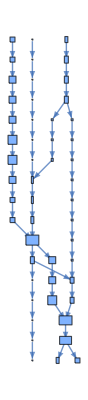
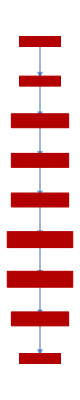
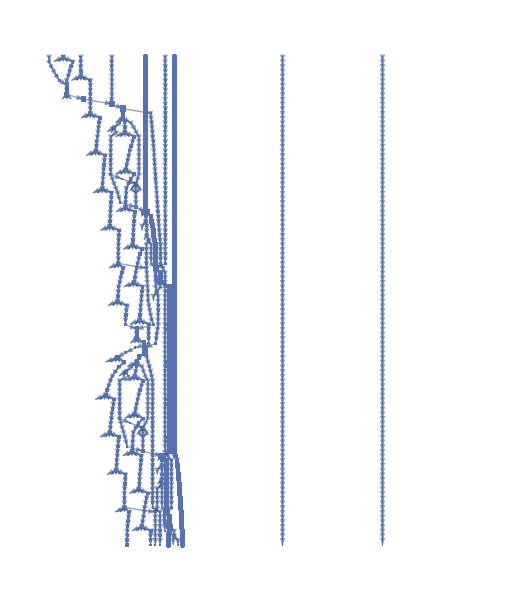

```mathematica
HighlightGraph[#[[2]], 
VertexList[#[[2]]][[
(Function[{left, right},With[{common=Intersection[left,right]},{Flatten[Position[left,#]&/@common],Flatten[Position[right,#]&/@common]}]]@@
(Map[
(SparseArray[
Thread[
(Transpose[{#[[All, 1]] -  Min[#[[All, 1]]]+1, #[[All, 2]] -  Min[#[[All, 2]]]+1}]&[
Ramp[#[[-1]] ]]+ 1)->1]]&), 
VertexList/@ #, {2}]))[[2]]]]]&@ {m, BoundingBoxLayeredGraph[$LifeData[#]]}&/@ Take[Keys[$LifeParts["Oscillator"]][[Catenate[Position[mat[[TakeLargestBy[Range[Length[mat]], Total[mat[[#]]]&, 20][[2]]]], 1]]]], 3]
```

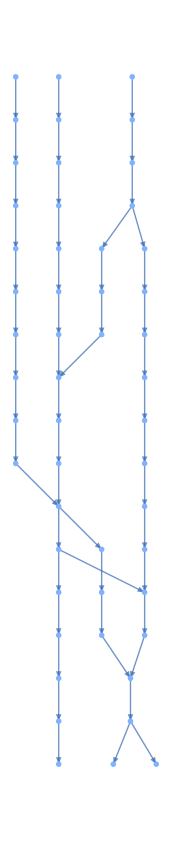
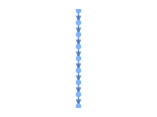

```mathematica
PatternsLayeredGraph[$LifeData[#]]&/@Take[Keys[$LifeParts["Oscillator"]][[Catenate[Position[mat[[TakeLargestBy[Range[Length[mat]], Total[mat[[#]]]&, 20][[2]]]], 1]]]], 2]
```

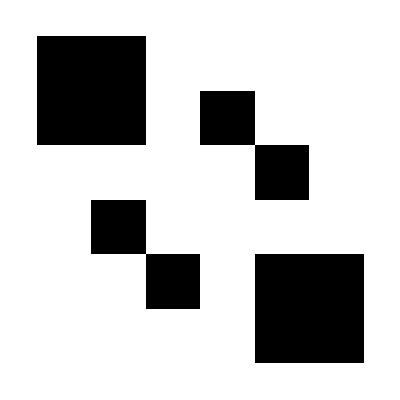

```mathematica
ArrayPlot[PatternCanonicalize[#MatrixData]&[$LifeData["Figure eight"]]]
```

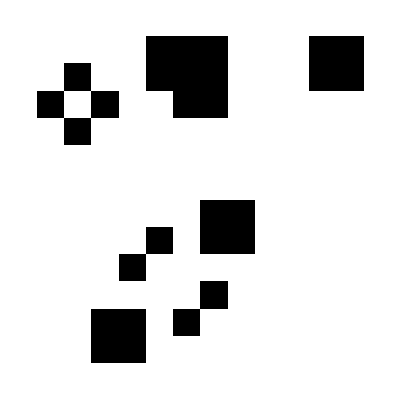

```mathematica
ArrayPlot[PatternCanonicalize[#MatrixData]&[$LifeData["Charity's p16"]]]
```

```mathematica
Keys[$LifeParts["Oscillator"]][[Catenate[Position[mat[[TakeLargestBy[Range[Length[mat]], Total[mat[[#]]]&, 20][[2]]]], 1]]]][[1]]
```

Charity's p16

```mathematica
ArrayPlot[First[Sort[ResourceFunction["ArrayRotations"][#]]]&[#["MatrixData"]]&[$LifeData["Figure eight"]]]
```

-Graphics-

```mathematica
ArrayPlot[First[Sort[ResourceFunction["ArrayRotations"][#]]]&[#["MatrixData"]]&[$LifeData["Charity's p16"]]]
```

-Graphics-

### Highlighting patterns

```mathematica
CellularAutomatonHistoryPlot["GameOfLife", {#MatrixData, 0}, #Period]&[$LifeData[Keys[$LifeParts["Oscillator"]][[TakeLargestBy[Range[Length[mat]], Total[mat[[#]]]&, 20][[2]]]]]]
```

-Graphics-

```mathematica
CellularAutomatonHistoryPlot["GameOfLife", {#MatrixData, 0}, #Period]&[$LifeData[#]]&/@ Keys[$LifeParts["Oscillator"]][[Catenate[Position[mat[[TakeLargestBy[Range[Length[mat]], Total[mat[[#]]]&, 20][[2]]]], 1]]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Matall

```mathematica
matall = CloudImport["https://www.wolframcloud.com/obj/e7ebcbbe-efed-4c19-850c-b8df05128b0c"];
```

CloudObject::invuri: The URI https://www.wolframcloud.com/obj/e7ebcbbe-efed-4c19-850c-b8df05128b0c is not valid.

```mathematica
["https://www.wolframcloud.com/obj/e7ebcbbe-efed-4c19-850c-b8df05128b0c"](https://www.wolframcloud.com/obj/e7ebcbbe-efed-4c19-850c-b8df05128b0c)
```

https://www.wolframcloud.com/obj/e7ebcbbe-efed-4c19-850c-b8df05128b0c

```mathematica
matall = CloudImport[["https://www.wolframcloud.com/obj/e7ebcbbe-efed-4c19-850c-b8df05128b0c"](https://www.wolframcloud.com/obj/e7ebcbbe-efed-4c19-850c-b8df05128b0c)];
```

```mathematica
ArrayPlot[matall]
```

-Graphics-

```mathematica
diffs = DeleteCases[Position[matall,1],{x_,x_}];
```

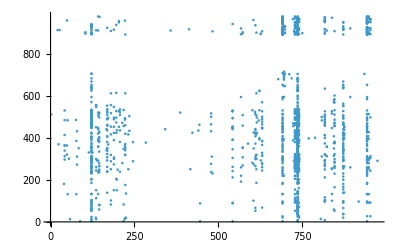

```mathematica
ListPlot[diffs]
```

```mathematica
apsi=Select[Catenate[Values[$LifeParts[#]]&/@Keys[$LifeParts]],Length[#]<300&&Times@@Dimensions[#[[-1]]]<=1000&->"Index"];
```

```mathematica
aps=Select[Catenate[Values[$LifeParts[#]]&/@Keys[$LifeParts]],Length[#]<300&&Times@@Dimensions[#[[-1]]]<=1000&];
```

```mathematica
Select[Catenate[Values[$LifeParts[#]]&/@Keys[$LifeParts]],Length[#]<300&&Times@@Dimensions[#[[-1]]]<=1000&->"Index"]
```

```mathematica
namesall = Select[Join[$LifeParts[#]&/@Keys[$LifeParts]],Length[#]<300&&Times@@Dimensions[#[[-1]]]<=1000&->"Index"];
```

Part::partd: Part specification 101⟦-1⟧ is longer than depth of object.

Part::partd: Part specification 104P9⟦-1⟧ is longer than depth of object.

Part::partd: Part specification 106P135⟦-1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
names = Select[Join@@($LifeParts[#]&/@Keys[$LifeParts]), Length[#]<300&&Times@@Dimensions[#[[-1]]]<=1000&];
```

```mathematica
top = CellularAutomatonHistoryPlot["GameOfLife", {#[[-1]], 0}, 2Length[#]]&/@Values[$LifeParts["Oscillator"]][[TakeLargestBy[Range[Length[mat]], Total[mat[[#]]]&, 20]]];
```

```mathematica
Values[$LifeParts["Oscillator"]][[TakeLargestBy[Range[Length[mat]], Total[mat[[#]]]&, 20]]]
```

```mathematica
TakeLargestBy[Range[Length[matall]], Total[matall[[#]]]&, 20]
```

{737,122,692,944,729,873,741,818,169,543,847,631,145,949,142,611,954,696,136,180}

```mathematica
names[[TakeLargestBy[Range[Length[matall]], Total[matall[[#]]]&, 20]]]
```

{Block,Blinker,Glider,Three-block shifter,Beehive,Tub,Boat,Loaf,Figure eight,Pentadecathlon,Snake,Unix,Clock,Silver's reflector,Chucklebait,Toad,CC semi-Snark,Lightweight spaceship,Caterer,Fumarole}

```mathematica
$LifeData[names[[TakeLargestBy[Range[Length[matall]], Total[matall[[#]]]&, 20]]]]
```

Missing[KeyAbsent,{Block,Blinker,Glider,Three-block shifter,Beehive,Tub,Boat,Loaf,Figure eight,Pentadecathlon,Snake,Unix,Clock,Silver's reflector,Chucklebait,Toad,CC semi-Snark,Lightweight spaceship,Caterer,Fumarole}]

Note the nice mesh scaling here, maybe SW wants this as default?

```mathematica
top = CellularAutomatonHistoryPlot["GameOfLife", {#MatrixData, 0}, Replace[#[["Period"]], _Missing-> 1], MeshStyle->Opacity[(.25/(Times@@Dimensions[#MatrixData])^.3)], "Decay"-> .9]&[$LifeData[#]]&/@names[[TakeLargestBy[Range[Length[matall]], Total[matall[[#]]]&, 20]]];
```

```mathematica
top2 = CellularAutomatonHistoryPlot["GameOfLife", {#[[-1]], 0}, Length[#]]&/@aps[[TakeLargestBy[Range[Length[matall]], Total[matall[[#]]]&, 20]]];
```

```mathematica
With[{tots = ReverseSort[Total/@ matall]},
ListLogLogPlot[ReplacePart[tots/Total[tots],Table[i-> Callout[tots[[i]]/Total[tots], top2[[i]]], {i, 1, 20}]], Frame-> True, FrameLabel->{"rank", "frequency"} ]
 ]
```

-Graphics-

Over time

```mathematica
CellularAutomatonHistoryPlot["GameOfLife", {#MatrixData, 0}, #Period]&[$LifeData[#]]&/@ Keys[$LifeParts["Oscillator"]][[Catenate[Position[mat[[#]], 1]]]]&/@
```

```mathematica
TakeLargestBy[Range[Length[matall]], Total[matall[[#]]]&, 20]
```

{737,122,692,944,729,873,741,818,169,543,847,631,145,949,142,611,954,696,136,180}

```mathematica
usednames = names[[Catenate[Position[matall[[#]], 1]]]]&/@TakeLargestBy[Range[Length[matall]], Total[matall[[#]]]&, 20];
```

```mathematica
BubbleChart[MapAt[Callout[#,names[[TakeLargestBy[Range[Length[matall]], Total[matall[[#]]]&, 20]]][[#[[2]]]], LabelVisibility->All]&, # ,1]&/@ 
(KeyValueMap[Append[#1, #2]&, #]&/@ Counts/@(Sort/@ MapIndexed[{$LifeData[#]["Year"], First[#2]}&, usednames, {2}]))]
```

-Graphics-

```mathematica
BubbleChart[
(KeyValueMap[Append[#1, #2]&, #]&/@ Counts/@(Sort/@ MapIndexed[{$LifeData[#]["Year"], First[#2]}&, usednames, {2}])), FrameTicks-> {{Transpose[{Range[20], names[[TakeLargestBy[Range[Length[matall]], Total[matall[[#]]]&, 20]]]}], Automatic}, {Automatic, Automatic}}, PlotLabel->"Usage over time"]
```

-Graphics-